```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
testArena[n_] := Module[{arena,θ},
θ=N[π/8];
arena=<|
"Type"->"Cone",
"DiskRadius"->1,
"ConeSemiAngle"->θ,
"Edges"-><|"Left"->InfiniteLine[{{0,0},{-Sin[θ],Cos[θ]}}],"Right"->InfiniteLine[{{0,0},{Sin[θ],Cos[θ]}}]|>,
"zRange"->{0,30},
"IDmax"->n
|>;
arena
];
```

```mathematica
restartRun[lastRun_] := Module[{},
run=lastRun;


run["Logging"]["Disks"]=<||>;
run["Logging"]["ChainStore"] = {};

globalTime=Now;
globalTangentDiskCache=<||>;
monitorString="Restart";

run=Monitor[
NestWhile[
addLowest,run,continueCondition,1,maxIterations=1000],monitorString];
Print[monitorString];
run
]
continueCondition[run_] := Module[{diskID},
diskID=Max[Select[Keys[run["Disks"]],NumberQ]];
If[diskID>= run["Arena"]["IDmax"], Return[False]];
Return[True]
]
```

```mathematica
run40=doParameterisedRun[testArena[11]];
```

11 	<|Up -> 2, Down -> 3|> 	Elapsed 0 s	Timing 16

401 	<|Up -> 13, Down -> 21|> 	Elapsed 18 s	Timing 31

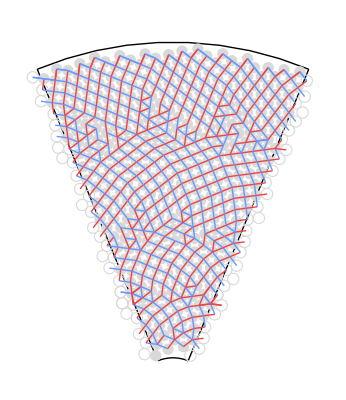

```mathematica
restart=run40;
restart["Arena"]["IDmax"]=401;
run50=restartRun[restart];
displayRun[run50]
```

```mathematica
doParameterisedRun[arena_] := Module[{},
runDisks=initalizeDisks[arena];
runChain={left[1],1,right[1]};

run=<|
"Arena"->arena,
"Disks"->runDisks,
"Chain"->runChain,
"ID"->1,
"Logging"-><|
"ID"->1,
"Disks"-><||>,
"ChainStore"->{runChain},
"ParastichyCount"-><|1-><|"Up"->1,"Down"->1|>|>,
"rMax"->"Missing"
|>
|>;
run=logStep[run,0];
run=restartRun[run];
run
]

logStep[run_,timing_] := Module[{res,thisLog,elapsed},
res=run;
thisLog=res["Logging"];

elapsed=Round@Abs@DateDifference[Now,globalTime,"Second"];
thisLog["ElapsedSeconds"]=Round@Abs@DateDifference[Now,globalTime,"Second"];
thisLog["TimingMicroSeconds"]=Round[1000*timing];

thisLog["ID"]=run["ID"];
thisLog["Disks"]=Append[thisLog["Disks"],run["Disks"]];
thisLog["ChainStore"]=Append[thisLog["ChainStore"],run["Chain"]];
res["Logging"]=thisLog;

(* computeParastichy needs the disks in res["Logging"]["Disks"] *)
thisLog["ParastichyCount"] =Append[thisLog["ParastichyCount"] ,res["ID"]->computeParastichy[res]];
res["Logging"]=thisLog;
res
]

monitoringString[run_] := Module[{},
StringTemplate[
" `ID` \t`Parastichy pair` \tElapsed `ElapsedSeconds`\tTiming `TimingMicroSeconds`"]
[Append[run["Logging"],"Parastichy pair"->Last@run["Logging"]["ParastichyCount"]]]
];
```

```mathematica
addLowest[run_] := Module[{res,ixPairs,ID,ids,diskData,disks,timing,monitorResults},
res=run;
ID=run["ID"]+1;
res["ID"]=ID;

{timing,diskData}=Timing[lowestTangentDiskFromPairs[res,ID]];

res["Disks"]= addDisk[res["Arena"],res["Disks"],diskData,ID];
res["Chain"]= updateChain[res,diskData];

clearOldDisksFromCache[res];

(* if the new disk has a supporter which is a left[n] or right[n] that might not have been in the Disks before, because it was only there as n   *)
ids=Complement[res["Chain"],Keys[res["Disks"]]];
res["Disks"]=Fold[addLRDisk[res["Arena"],#1,#2]&,res["Disks"],ids];

res=logStep[res,timing];

(* having logged past disks, only use current chain for lookup *)
res["Disks"]=KeyTake[res["Disks"],Append[res["Chain"],ids]];

monitorString=monitoringString[res];

res

];
```

## Computation: fixed radius disk on cone

```mathematica
initalizeDisks[arena_] := Module[{initialDisks,d},
d=N[arena["DiskRadius"]/Sin[arena["ConeSemiAngle"]]];
initialDisks=<|1-><|"ID"->1,"Disk"->Disk[{0,d},arena["DiskRadius"]]
,"Polar"-><|"r"->d,"θ"->π/2|>
,"Supporters"->Missing[]
,"EdgeDisk"-><|"Left"->True,"Right"->True|>
,"CanSupportDisk"-><|"Left"->True,"Right"->True|>
|>|>;
initialDisks=addLRDisk[arena,initialDisks,left[1]];
initialDisks=addLRDisk[arena,initialDisks,right[1]];
initialDisks
];
```

```mathematica
addDisk[arena_,disks_,disk_,ID_] := Append[disks,ID->disk];
addLRDisk[arena_,disks_,left[ID_]] := Append[disks,left[ID]->leftShift[arena,Lookup[disks,ID]]];
addLRDisk[arena_,disks_,right[ID_]] := Append[disks,right[ID]->rightShift[arena,Lookup[disks,ID]]]
```

```mathematica
leftQ[n_] := Head[n]===left;
rightQ[n_] := Head[n]===right;
shiftNumberRight[left[n_]] :=n;
shiftNumberRight[n_] :=right[n];

shiftNumberLeft[right[n_]] :=n;
shiftNumberLeft[n_] := left[n];

leftShift[left[n_]]:= shiftNumberLeft[left[n]];
leftShift[right[n_]] := shiftNumberLeft[right[n]];
leftShift[n_Integer] := shiftNumberLeft[n];
rightShift[left[n_]]:= shiftNumberRight[left[n]];
rightShift[right[n_]] := shiftNumberRight[right[n]];
rightShift[n_Integer] := shiftNumberRight[n];


leftShift[arena_,xy_List] := RotationTransform[2 arena["ConeSemiAngle"]][xy];
rightShift[arena_,xy_List] := RotationTransform[-2 arena["ConeSemiAngle"]][xy];

leftShift[arena_,Disk[xy_,r_]] := Disk[leftShift[arena,xy],r];
rightShift[arena_,Disk[xy_,r_]] := Disk[rightShift[arena,xy],r];

leftShift[arena_,data_Association] := <|
"ID"->shiftNumberLeft[data["ID"]]
,"Disk"->leftShift[arena,data["Disk"]]
,"Polar"->leftPolar[arena,data["Polar"]]
,"Supporters"->shiftNumberLeft/@data["Supporters"]
,"EdgeDisk"-> <|"Left"->False,"Right"->False|>
,"CanSupportDisk"-><|"Left"->False,"Right"->False|>
|>;
rightShift[arena_,data_Association] := <|
"ID"->shiftNumberRight[data["ID"]],
"Disk"->rightShift[arena,data["Disk"]]
,"Polar"->rightPolar[arena,data["Polar"]]
,"Supporters"->shiftNumberRight/@data["Supporters"]
,"EdgeDisk"-> <|"Left"->False,"Right"->False|>
,"CanSupportDisk"-><|"Left"->False,"Right"->False|>
|>;
leftPolar[arena_,polar_Association] := Append[polar,"θ"->polar["θ"]+2 arena["ConeSemiAngle"]]
rightPolar[arena_,polar_Association] := Append[polar,"θ"->polar["θ"]-2 arena["ConeSemiAngle"]]
```

```mathematica
lowestTangentDiskFromPairs[run_,ID_]:= 
Module[{choices,arena,chainDisks,ixPairs,lowest,ict},
arena=run["Arena"];

ixPairs=findSupportingPairs[run];

choices= Map[<|"Disk"->findTangentDisk[run,#],"Supporters"->#|>&,ixPairs];

choices=Select[choices,!MissingQ[#Disk]&];
choices=computeOverlapping[run,choices];
updateDiskPairCache[choices];
choices=Select[choices,!#Overlapping&];
choices=Map[Append[#,"Polar"->disk2Polar[#Disk]]&,choices];

choices=SortBy[choices,#["Polar"]["r"]&];


lowest=First[choices];
lowest=Prepend[lowest,"ID"->ID];

ict=inConeType[run["Arena"],lowest];

If[ict=="Left",
lowest=rightShift[arena,lowest]
];
If[ict=="Right",
lowest=leftShift[arena,lowest]
];
lowest["ID"]=ID;
lowest=computeEdgeProperties[run["Arena"],lowest];
lowest
];

computeEdgeProperties[arena_,disk_] := Module[{distance,edgeDisk,supporterDisk},
(* for algorithm purposes, is it close enough to the left (right) edge to act as a supporter over the left (right_ edge  *)
distance=distanceFromDiskToEdge[arena,disk];
supporterDisk=Map[ #< 2arena["DiskRadius"]&,distance ];
(* for display purposes is it on the edge *)
edgeDisk=Map[#<arena["DiskRadius"]&,distance];
Append[disk,<|"EdgeDisk"->edgeDisk,"CanSupportDisk"->supporterDisk|>]
];

distanceFromDiskToEdge[arena_,disk_] := Module[{},
(*assumes linear cone *)
Association@Map[#->RegionDistance[arena["Edges"][#],diskCentre[disk["Disk"]]]&,Keys[arena["Edges"]]]
];
```

```mathematica
findTangentDisk[run_,{idx1_,idx2_}]:=Module[{xy},
(* xy of centre, or Missing[...] if either too far apart for a disk, or the disk overlaps one already found *)
If[KeyMemberQ[globalTangentDiskCache,{idx1,idx2}],
Return[globalTangentDiskCache[{idx1,idx2}]]];

xy=findUncachedTangentDisk[run,{idx1,idx2}];
globalTangentDiskCache[{idx1,idx2}]=xy;
xy

];

updateDiskPairCache[choices_] := Module[{overlaps,overlapPairs},
overlaps=Select[choices,#Overlapping&];
overlapPairs=Map[#Supporters&,overlaps];
Map[(globalTangentDiskCache[#]=Missing["Overlap"])&,overlapPairs];
];

clearOldDisksFromCache[run_] :=  Module[{cacheKeyActive},
(* if the chain has been updated, we can make the cache smaller and faster to search; may or may not make a difference  *)
cacheKeyActive[{ix1_,ix2_}] := ( MemberQ[run["Chain"],ix1] &&MemberQ[run["Chain"],ix2]);

globalTangentDiskCache=KeySelect[globalTangentDiskCache,cacheKeyActive];
];
```

```mathematica
findUncachedTangentDisk[run_,{idx1_,idx2_}]:=Module[{c1,c2,R,centres},

c1=runDiskCentre[run,idx1];
c2=runDiskCentre[run,idx2];
R=run["Arena"]["DiskRadius"];
centres=tangentDiskCentres[c1,c2,R];
If[centres==Missing["Identical"],
Print["Identical",{idx1,idx2}](*;Abort[]*)];
(* two touchhing disks are possible, above and below starting pair; always want above and rely on origin of cone at (0,) so that the largest Norm is the one we want *)

centres=SortBy[centres,Norm];
If[Length[centres]==0,
Return[Missing["No tangent pair"]]
];
Disk[Last[centres],R]
];

computeOverlapping[run_,choices_] := Module[{res},
res=Map[Append[#,"Overlapping"->
diskIDDiskDistance[run["Arena"],run["Disks"],#]<  2 run["Arena"]["DiskRadius"]
]&,choices];

res
];
```

```mathematica
findSupportingPairs[run_] := Module[{ixPairs,bare,leftRightSupportable,leftSupportable,rightSupportable},
ixPairs=Select[run["Chain"],NumberQ];
leftRightSupportable=Map[#CanSupportDisk&,KeyTake[run["Disks"],ixPairs]];
leftSupportable=Keys[Select[leftRightSupportable,#Left&]];
leftSupportable=right/@leftSupportable;
rightSupportable=Keys[Select[leftRightSupportable,#Right&]];
rightSupportable=left/@rightSupportable;
ixPairs=Join[rightSupportable,ixPairs,leftSupportable];

ixPairs=Subsets[ixPairs,{2}]
];
```

```mathematica
updateChain[run_,disk_] := Module[{ID,supporters,chainGraph,chainNumbers,from,to,outSplice,debug},
ID=disk["ID"];



supporters=disk["Supporters"];
chainNumbers=run["Chain"];
{from,to}=Map[fom@fom@Position[chainNumbers,#,1]&,supporters];
If[from>to,supporters=Reverse[supporters]];
If[leftQ[supporters[[1]]],chainNumbers[[1]]=supporters[[1]]];
If[rightQ[supporters[[2]]],chainNumbers[[-1]]=supporters[[2]]];
chainNumbers=listReplaceRange[chainNumbers,supporters[[1]],supporters[[2]],{supporters[[1]],ID,supporters[[2]]}];
If[rightQ[supporters[[2]]],
chainNumbers=listReplaceRange[chainNumbers,First[chainNumbers],shiftNumberLeft[supporters[[2]]],{shiftNumberLeft[ID],shiftNumberLeft[supporters[[2]]]}];
];
If[leftQ[supporters[[1]]],
If[supporters[[1]] != First[chainNumbers],
Print["uC ",chainNumbers]];
chainNumbers=listReplaceRange[chainNumbers,
shiftNumberRight[supporters[[1]]],Last[chainNumbers],{shiftNumberRight[supporters[[1]]],shiftNumberRight[ID]}];
];
chainNumbers
];
```

```mathematica
listIndex[list_,x_] := Module[{res},
res=Position[list,x,1];
If[Length[res]==0,Return[Missing[]]];
res=First@First[res];
res
];
```

```mathematica
listReplaceRange[list_,s_,f_,rep_]:= list/. {before___,s,___,f,after___}:>({before,Splice[rep],after});
```

```mathematica
diskCentre[Disk[centre_,radius_]]:=centre;
diskTop[Disk[centre_,radius_]]:=centre+radius;
(*diskIDCentre[arena_,disks_,id_] := diskCentre@Lookup[disks,id]["Disk"];
*)
diskIDCentre[disks_,id_] := diskCentre@Lookup[disks,id]["Disk"];

runDiskCentre[run_,id_] :=  diskCentre@Lookup[run["Disks"],id]["Disk"];
runDiskCentre[run_,left[id_] ] := leftShift[run["Arena"],runDiskCentre[run,id]];
runDiskCentre[run_,right[id_] ] := rightShift[run["Arena"],runDiskCentre[run,id]];

disk2Polar[Disk[{x_,y_},_]]:= <|"r"->Norm[{x,y}],"θ"->ArcTan[x,y]|>;

diskIDRadialHeight[run_,id_] :=  Lookup[run["Logging"]["Disks"],id]["Polar"]["r"];

fom[x_]:= If[Length[x]>0,First[x],Missing[x]];
```

```mathematica
computeParastichy[run_] := Module[{edges,res},
edges=chainEdges[run,Drop[run["Chain"],-1]];

res=parastichyCount[Values[edges]];

res
];
```

```mathematica
chainEdges[run_,chain_] :=  Module[{edges,graph,pairs,nodes},
pairs=Partition[chain,2,1];
edges=Map[Apply[UndirectedEdge,#]&,pairs];
edges=Association@Map[#->orientation[run,#]&,edges]
];

orientation[run_,a_ <-> b_] := Module[{radii},
radii=diskIDRadialHeight[run,#]&/@{a,b};
If[radii[[1]]<radii[[2]],"Up","Down"]
]

orientationStyle["Up"]:= StandardRed;
orientationStyle["Down"]:= StandardBlue;


parastichyCount[updowns_] := Module[{res},
res= updowns;
res=Counts[updowns,{"Up","Down"}];
res
]
```

## Display

```mathematica
makeLine[run_,p_ <-> q_ , orientation_] :=  Module[{},
{orientationStyle[orientation],Line[{diskIDCentre[run["Logging"]["Disks"],p],diskIDCentre[run["Logging"]["Disks"],q]}]}
];


makeLines[run_] :=  Module[{chains,diskCentres},
chains=run["Logging"]["ChainStore"];
edgeSet=Join@@Flatten[Map[chainEdges[run,#]&,chains]];
KeyValueMap[makeLine[run,#1,#2]&,edgeSet]
];

makeTopChainLine[run_] :=  Module[{chains,diskCentres},
chains=Take[run["Logging"]["ChainStore"],-1];
edgeSet=Join@@Flatten[Map[chainEdges[run,#]&,chains]];
KeyValueMap[makeLine[run,#1,#2]&,edgeSet]
];
```

```mathematica
displayCone[arena_,rMinMax_] := Module[{xMin,xMax,zMin,zMax},
{xMin,xMax}=rMinMax*Sin[arena["ConeSemiAngle"]];
{zMin,zMax}=rMinMax*Cos[arena["ConeSemiAngle"]];
{Line[{{xMin,zMin},{xMax,zMax}}]
,Line[{{-xMin,zMin},{-xMax,zMax}}]
,Circle[{0,0},rMinMax[[1]],{π/2-arena["ConeSemiAngle"],π/2+arena["ConeSemiAngle"]}]
,Circle[{0,0},rMinMax[[2]],{π/2-arena["ConeSemiAngle"],π/2+arena["ConeSemiAngle"]}]
}
];
```

```mathematica
lom[x_] := If[MissingQ[x],{},x];
labelledDisk[disk_] := {disk["Disk"],Text[disk["ID"],diskCentre[disk["Disk"]]]}
unlabelledDisk[disk_] := {disk["Disk"]}
diskClassify[run_] := Module[{},
plainDisks=Values@Select[run["Logging"]["Disks"],NumberQ[#ID]&];
byEdge=GroupBy[plainDisks,(#EdgeDisk&)->(KeyTake[#,{"ID","Disk"}]&)];
rightEdgeDisks=lom@byEdge[<|"Left"->False,"Right"->True|>];
rightEdgeDisksLeft=leftShift[run["Arena"],#]&/@rightEdgeDisks;
leftEdgeDisks=lom@byEdge[<|"Left"->True,"Right"->False|>];
leftEdgeDisksRight=leftShift[run["Arena"],#]&/@rightEdgeDisks;

rightsupporterDisks=Select[plainDisks,#CanSupportDisk["Right"]&];
rightsupporterDisksLeft=leftShift[run["Arena"],#]&/@rightsupporterDisks;


leftsupporterDisks=Select[plainDisks,#CanSupportDisk["Left"]&];
leftsupporterDisksRight=rightShift[run["Arena"],#]&/@leftsupporterDisks;

{{ FaceForm[LightGray],EdgeForm[None],unlabelledDisk/@  byEdge[<|"Left"->False,"Right"->False|>]}
,
{ FaceForm[LightGray],EdgeForm[None],unlabelledDisk/@  rightEdgeDisks,unlabelledDisk/@  leftEdgeDisks}
,
{FaceForm[None],EdgeForm[LightGray],unlabelledDisk/@rightsupporterDisksLeft,unlabelledDisk/@leftsupporterDisksRight}
(*,{ FaceForm[LightGray],EdgeForm[None],unlabelledDisk/@  rightEdgeDisksLeft,unlabelledDisk/@ leftEdgeDisksRight}
*)
}

(*,GroupBy[Values[run["Disks"]],#CanSupportDisk&]*)

];
```

```mathematica
displayRun[run_]:=Module[{lines,topChainLines,disks,styledDisks,rMinMax},
disks= Values@run["Logging"]["Disks"];
rMinMax=MinMax[Map[#Polar["r"]&,disks]];
rMinMax=rMinMax+{-run["Arena"]["DiskRadius"],run["Arena"]["DiskRadius"]};
xMax=rMinMax[[2]]* Sin[run["Arena"]["ConeSemiAngle"]]+run["Arena"]["DiskRadius"];

styledDisks= diskClassify[run];

lines=makeLines[run];
topChainLines=makeTopChainLine[run];



Show[Graphics
[{
displayCone[run["Arena"],rMinMax],
{styledDisks},
lines,
Thick,topChainLines
(*displayDiskNumbers[arena,disks,Keys[disks]]
*)
},PlotRange->{{-xMax,xMax},rMinMax+{-run["Arena"]["DiskRadius"],run["Arena"]["DiskRadius"]}}]]
]
displayDiskNumbers[arena_,disks_,diskIDs_]:={ EdgeForm[{Thin,Gray}],FaceForm[Lighter[Blue,0.98]],
Map[displayDiskNumber[arena,disks,#]&,diskIDs]
};

displayDiskNumber[arena_,disks_,diskID_]:= Module[{disk},
disk=Lookup[disks,diskID]["Disk"];
{disk,Text[diskID,diskCentre[disk]]}
];
```

## Touching disk computation

```mathematica
inConeType[arena_,diskData_] := Which[
diskData["Polar"]["θ"] < π/2 -  arena["ConeSemiAngle"] ,"Right",
diskData["Polar"]["θ"] > π/2 +  arena["ConeSemiAngle"] ,"Left",
True,"Centre"]
```

```mathematica
segment[arena_,polar_] := Circle[{0,0},polar["r"],{π/2-1.5 arena["ConeSemiAngle"],π/2+1.5 arena["ConeSemiAngle"]}];
```

```mathematica
diskIDDiskDistance[arena_,disks_,disk_] := Module[{c1,diskCentres,cLeft,cRight},
c1=diskCentre[disk["Disk"]];
cLeft=leftShift[arena,c1];
cRight=rightShift[arena,c1];
diskCentres=Map[diskIDCentre[disks,#]&,Keys[disks]];
Min@Flatten[{
Map[Norm[#-c1]&,diskCentres],Map[Norm[#-cLeft]&,diskCentres],Map[Norm[#-cRight]&,diskCentres]
}
]
];
```

```mathematica
tangentDiskCentres[c1_List,c2_List,R_]:=Module[{mid,diff,d,h,hSquared,unitPerp},
(*1. Vector between centers and total distance*)
diff=c2-c1;
d=Norm[diff];
If[Chop[d]==0,Print["tDC Identical ",c1];Return[Missing["Identical"]]];

(*2. Check if a solution exists (distance must be<=4R)*)
hSquared=4*R^2-(d/2)^2;
If[hSquared<0,
Return[Missing[]]
];
(*3. Midpoint and the height of the triangle from midpoint to c3*)
mid=(c1+c2)/2;
h=Sqrt[hSquared];
(*4. Find the unit vector perpendicular to the line connecting c1 and c2*)(*Standard 2D rotation:{x,y}->{-y,x}*)
unitPerp={-diff[[2]],diff[[1]]}/d;
(*5. Return the two possible centers*)
{mid+h*unitPerp,mid-h*unitPerp}
]
```

# Printout to scale

```mathematica
testScale[] := Module[{},
imageSizeInPoints=20*28.35;
g=testRun[15];
scale=Show[g,Graphics[{Thick,Black,Line[{{1,1},{2,1}}]}],Axes->True,PlotRange->{{-10,10},{0,29}}];
Export["graphic.pdf",g,ImageSize->imageSizeInPoints]
]
```